```mathematica
wd=NotebookDirectory[];
appPath="+mem="<>wd<>"dhrystone.bin";
```

```mathematica
LibraryUnload[libhello]
```

```mathematica
<<"/Users/ckorikov/_syntacore/projects/wolfram_russianhack18_scr1/cpp_bridge/math.m"
```

```mathematica
pclist = Table[nextpc[],10000];
```

```mathematica
g=BlockMap[#[[1]]->#[[2]]&,pclist,2,1];
```

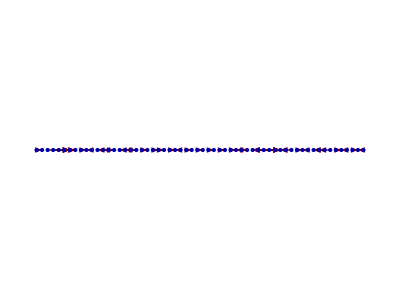

```mathematica
GraphPlot[Select[g,(#[[2]]-#[[1]])>100&],DirectedEdges-> True,Method->"LinearEmbedding"]
```

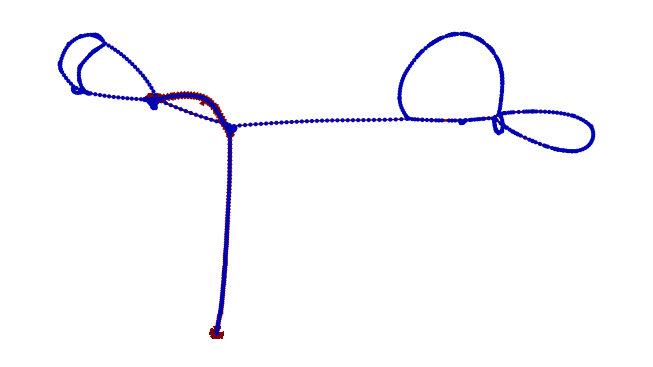

```mathematica
GraphPlot[g[[2000;;9000]],DirectedEdges-> True]
```

```mathematica
Dataset[Table[{i,BaseForm[getregister[i],16],BaseForm[getregister[i],2]},{i,1,31}]]
```

Dataset[<>]

```mathematica
reset["+mem=/Users/ckorikov/_syntacore/projects/wolfram_russianhack18_scr1/cpp_bridge/dhrystone.bin"];
```

```mathematica
regs=Table[{i,getregister[i]},{i,1,31}];
```

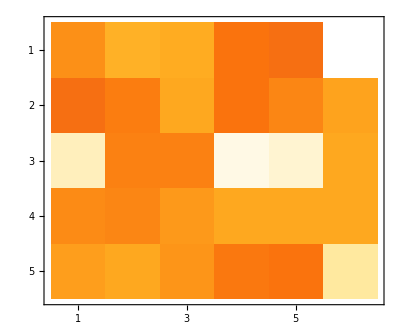

```mathematica
MatrixPlot[BlockMap[#&,Map[#[[2]]&,regs],6],ColorFunction->"SunsetColors"]
```

```mathematica
Table[nextpc[],10000];
```

```mathematica
ListAnimate[Table[nextpc[];MatrixPlot[BlockMap[#&,Map[#[[2]]&,Table[{i,getregister[i]},{i,1,31}]],6],ColorFunction->"SunsetColors"],
1000
]]
```

```mathematica
reglist = LibraryFunctionLoad[libhello, "get_register_list_register", {},{ Integer,1}];
```

LibraryFunction::libload: The function get_register_list_register was not loaded from the file /Users/ckorikov/Library/Mathematica/SystemFiles/LibraryResources/MacOSX-x86-64/hello.dylib.